```mathematica
SetDirectory["/Users/GregoryRidgway/Desktop/RHIC and Hydro/SimulatingHydroPlus"]
```

/Users/GregoryRidgway/Desktop/RHIC and Hydro/SimulatingHydroPlus

```mathematica
replaceZeros[m_?MatrixQ]:=Normal[SparseArray[m]/.HoldPattern[SparseArray[s___]]:>Module[{parts={s}},parts[[3]]=10.^-30;
SparseArray@@parts]];
```

Increase the relaxation rate until

```mathematica
dps//Dimensions
```

{0}

```mathematica
Nq=20;

dps=Partition[Partition[ReadList["!awk '/^dp/{print $2}' tmp", Number],Nq],512];
dps=replaceZeros/@dps;
dps=dps/Map[Total,dps,{2}];

ds=Partition[Partition[ReadList["!awk '/^rQ/{print $2}' tmp", Number],Nq],512];
ds=replaceZeros/@ds;
ds=ds/Map[Total,ds,{2}];

dbs=Partition[Partition[ReadList["!awk '/^rQ/{print $3}' tmp", Number],Nq],512];
dbs=replaceZeros/@dbs;
dbs=dbs/Map[Total,dbs,{2}];

Tfiles=ReadList["!ls ../data/snapshot/Tprofile_*",String];
len=Length[Tfiles];
times=Table[(ToExpression[#1]+.001ToExpression[#2])&@@StringSplit[StringSplit[Tfiles⟦k⟧,"_"]⟦2⟧,"."]⟦1;;2⟧,{k,len}];
max=times⟦Ordering[times,-1]⟦1⟧⟧;

greater=Position[times,x_/;x>10];
less=Position[times,x_/;x<10];

Recombine[L_List]:=(L⟦#⟧&@@@less)~Join~(L⟦#⟧&@@@greater);

times = Recombine[times];
Tfiles = Recombine[Tfiles];

Tlists = Table[ReadList[file,{Number,Number}],{file,Tfiles}];

Tlists=Tlists⟦Length[Tlists]-Length[dbs]+1;;⟧;
```

```mathematica
tim=1

tmp1 = (Max/@ds⟦tim,;;⟧)/.Indeterminate->0;
tmp2 = Max[tmp1];
tmp3=Position[tmp1-tmp2,_?(#==0&)]⟦1,1⟧;
(*Print["Position: ",tmp3*.25*.1973]*)
Print["T: ",Tlists⟦tim,tmp3⟧]
```

1

T: {10.3583,0.0356654}

- Fix the units!!! ✓ (double check)
- Same plot, but increase λ_M, normalize by s, and see that there’s inverse correlation
- make sure that the correlation length corresponds to mode 10-15
- plot inverse correlation length on the same plot (to see if it peaks in the correct general area).
- why did the first two modes have a big effect last week?

```mathematica
Position[ds[[1,1]],Max[ds[[1,1]]]]
```

{{4}}

```mathematica
{{15}}
```

```mathematica
(2*π(Range[4]-1)/512)^-1*.25*.1973
```

{ComplexInfinity,4.01936,2.00968,1.33979}

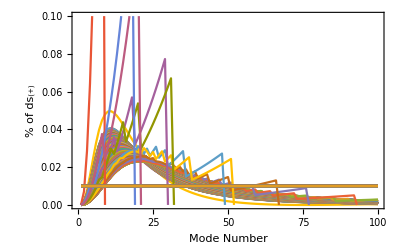

```mathematica
tim=1;
tmp3=511;
ListLinePlot[ds⟦tim,;;tmp3+1⟧,
(*PlotLabel->Style["τ="<>ToString[ϕTimes⟦tim⟧],20],*)FrameLabel->{Style["Mode Number",16], Style["% of ds_(+)", 16]}, PlotRange->{0,.1}]
```

```mathematica
tots="'{print "<>StringJoin@Table["$"<>ToString[3*i+1]<>", ",{i,2-1}]<>"$"<>ToString[3*2+1]<>"}' ";
ϕLists = Table[ReadList["!awk "<>tots<>ToString[file],Number],{file,ϕfiles⟦2;;⟧}];
```

```mathematica
Nq = 20;
mode=20;

ϕeqLists = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfiles⟦2;;⟧}];

ϕLists = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode+1]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfiles⟦2;;⟧}];
```

(1) Convince yourself that the erratic curves are just numerics,
(2) figure out where the UV cutoff is (Alternatively, find a λ_Msuch that NQ=20 is sufficient)
(3) Make sure that the apparent IR cutoff is consistent with your results

-Remember, the asymptotics of a Bessel function are a plane wave (So using the correct eigenfunctions is a subdominant effect)
-For example, we may look at 1/Q < 3fm at the beginning of the critical switching time, but no wavelengths greater (that’s not how Hydro+ was formulated)

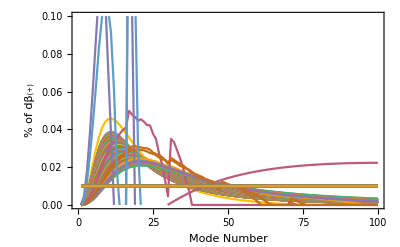

```mathematica
tim=1;
ListLinePlot[dbs⟦tim,;;⟧,FrameLabel->{Style["Mode Number",16], Style["% of dβ_(+)",16]}, PlotRange->{0,.1}]
```

```mathematica
tim=2;
ListLinePlot[dps⟦tim,;;⟧,FrameLabel->{Style["Mode Number",16], Style["% of dp_(+)", 16]}, PlotRange->{0,.1}]
```

ListLinePlot[{}⟦2,1;;All⟧,FrameLabel→{Mode Number,% of dp_(+)},PlotRange→{0,0.1}]

Snapshots

### Constants

```mathematica
t0 = .2;
ϵ0=.003;

Δ = .015;
σ = Δ*ϵ0/t0;
λM=5.1;
λM = 25.7;
λM = 1;
```

### Download Files

-s_(+) relative importance of each mode as a function of time

-p_(+)
-Evolution of hydro variables
-Evolution of ϕ

single-column, not microscopic font

Outline:
-Intro
-Summary of Hydro+
-Model (critical point, EoS, parametrization of relaxation rate)
-figures

```mathematica
512*(.25)/1*.1973
```

25.2544

```mathematica
.25*(.2)/1
```

0.05

```mathematica
Qs =  2*π *(Range[20]-1)/512
```

{0,π/256,π/128,(3 π)/256,π/64,(5 π)/256,(3 π)/128,(7 π)/256,π/32,(9 π)/256,(5 π)/128,(11 π)/256,(3 π)/64,(13 π)/256,(7 π)/128,(15 π)/256,π/16,(17 π)/256,(9 π)/128,(19 π)/256}

```mathematica
Qs =  (Range[27]-1)/512*1/(.25) * 1/(.1973);
1/Qs
```

{ComplexInfinity,25.2544,12.6272,8.41813,6.3136,5.05088,4.20907,3.60777,3.1568,2.80604,2.52544,2.29585,2.10453,1.94265,1.80389,1.68363,1.5784,1.48555,1.40302,1.32918,1.26272,1.20259,1.14793,1.09802,1.05227,1.01018,0.971323}

```mathematica
Abs[(plists⟦18⟧-ppluslists⟦18⟧)/plists⟦18⟧]⟦159⟧
```

{0.,0.0150448}

```mathematica
159*.25*.1978
```

7.86255

```mathematica
Max[Abs[(plists⟦18⟧-ppluslists⟦18⟧)/plists⟦18⟧]]
```

0.0151759

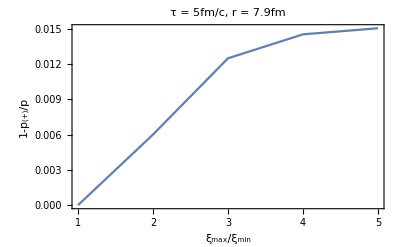

```mathematica
residPoints = {{1,0},{2, 0.006003816315673799},{3,0.012489750737946946},{4, 0.014525906205201737},{5, 0.015044829414811741}};
ListLinePlot[residPoints,
FrameLabel -> {Style["ξ_max/ξ_min",16],Style["1-p_(+)/p",16]},
PlotLabel->Style["τ = 5fm/c, r = 7.9fm",20]]
```

```mathematica
plists = Table[ReadList["!awk '{print $1, $2}' "<>ToString[file],{Number,Number}],{file,pfiles⟦;;⟧}];
(*plists0 = Table[ReadList["!awk '{print $1, $2}' "<>ToString[file],{Number,Number}],{file,pfiles0⟦5;;⟧}];*)
ppluslists = Table[ReadList["!awk '{print $1, $3}' "<>ToString[file],{Number,Number}],{file,pfiles⟦;;⟧}];
```

#### With backreaction

```mathematica
(*str="archiveNoBackreact/";*)
str="backreactArchive/";
str="archive_lam10/";
str = "largeXi5/";

(*SetDirectory["/Users/GregoryRidgway/Desktop/RHIC and Hydro/Original_Code"];*)
Tfiles=ReadList["!ls ../data/snapshot/"<>str<>"Tprofile_*",String];
vfiles=ReadList["!ls ../data/snapshot/"<>str<>"vprofile_*",String];
edfiles=ReadList["!ls ../data/snapshot/"<>str<>"edprofile_*",String];
pfiles=ReadList["!ls ../data/snapshot/"<>str<>"pplusprofile_*",String];
If[(λM==1) || (λM==0) || (λM == 10),
ϕfiles=ReadList["!ls ../data/snapshot/"<>str<>"Lam"<>ToString[λM]<>".0_Phiprofile_*",String];,
ϕfiles=ReadList["!ls ../data/snapshot/"<>str<>"Lam"<>ToString[λM]<>"_Phiprofile_*",String];
]
```

Order the T, v, and ϵ files

```mathematica
len=Length[Tfiles];
times=Table[(ToExpression[#1]+.001ToExpression[#2])&@@StringSplit[StringSplit[Tfiles⟦k⟧,"_"]⟦2⟧,"."]⟦1;;2⟧,{k,len}];
max=times⟦Ordering[times,-1]⟦1⟧⟧;

greater=Position[times,x_/;x>10];
less=Position[times,x_/;x<10];

Recombine[L_List]:=(L⟦#⟧&@@@less)~Join~(L⟦#⟧&@@@greater);

times = Recombine[times];
Tfiles = Recombine[Tfiles];
vfiles = Recombine[vfiles];
edfiles = Recombine[edfiles];
```

Order the ϕ and p files

```mathematica
ϕTimes = Table[(ToExpression[#1]+.001ToExpression[#2])&@@StringSplit[StringSplit[file,"_"]⟦3⟧,"."]⟦1;;2⟧,{file,ϕfiles}];

greater=Position[ϕTimes,x_/;x>10];
less=Position[ϕTimes,x_/;x<10];

Recombine[L_List]:=(L⟦#⟧&@@@less)~Join~(L⟦#⟧&@@@greater);

ϕTimes = Recombine[ϕTimes];
ϕfiles = (ϕfiles⟦#⟧&@@@less)~Join~(ϕfiles⟦#⟧&@@@greater);

pfiles = (pfiles⟦#⟧&@@@less)~Join~(pfiles⟦#⟧&@@@greater);
```

#### Same thing again, but now without backreaction

```mathematica
str="archiveNoBackreact/";
str="";
(*str="backreactArchive/";*)
(*str = "archive18/"*)

(*SetDirectory["/Users/GregoryRidgway/Desktop/RHIC and Hydro/Original_Code"];*)
Tfiles0=ReadList["!ls ../data/snapshot/"<>str<>"Tprofile_*",String];
vfiles0=ReadList["!ls ../data/snapshot/"<>str<>"vprofile_*",String];
edfiles0=ReadList["!ls ../data/snapshot/"<>str<>"edprofile_*",String];
pfiles0=ReadList["!ls ../data/snapshot/"<>str<>"pplusprofile_*",String];
If[(λM>=1) || (λM==0),
ϕfiles0=ReadList["!ls ../data/snapshot/"<>str<>"Lam"<>ToString[λM]<>".0_Phiprofile_*",String];,
ϕfiles0=ReadList["!ls ../data/snapshot/"<>str<>"Lam"<>ToString[λM]<>"_Phiprofile_*",String];
]
```

Order the T, v, and ϵ files

```mathematica
len=Length[Tfiles0];
times0=Table[(ToExpression[#1]+.001ToExpression[#2])&@@StringSplit[StringSplit[Tfiles0⟦k⟧,"_"]⟦2⟧,"."]⟦1;;2⟧,{k,len}];
max0=times0⟦Ordering[times0,-1]⟦1⟧⟧;

greater0=Position[times0,x_/;x>10];
less0=Position[times0,x_/;x<10];

Recombine[L_List]:=(L⟦#⟧&@@@less0)~Join~(L⟦#⟧&@@@greater0);

times0 = Recombine[times0];
Tfiles0 = Recombine[Tfiles0];
vfiles0 = Recombine[vfiles0];
edfiles0 = Recombine[edfiles0];
```

Order the ϕ and p files

```mathematica
ϕTimes0 = Table[(ToExpression[#1]+.001ToExpression[#2])&@@StringSplit[StringSplit[file,"_"]⟦3⟧,"."]⟦1;;2⟧,{file,ϕfiles0}];

greater0=Position[ϕTimes0,x_/;x>10];
less0=Position[ϕTimes0,x_/;x<10];

Recombine[L_List]:=(L⟦#⟧&@@@less0)~Join~(L⟦#⟧&@@@greater0);

ϕTimes0 = Recombine[ϕTimes0];
ϕfiles0= (ϕfiles0⟦#⟧&@@@less0)~Join~(ϕfiles0⟦#⟧&@@@greater0);

pfiles0 = (pfiles0⟦#⟧&@@@less0)~Join~(pfiles0⟦#⟧&@@@greater0);
```

### ϵ, T, and p movies

```mathematica
ϵlists[[1,{1,150}]]
```

{{0.049325,0.187251},{7.39876,0.00413855}}

```mathematica
Tlists[[1,{1,150}]]
```

{{0.049325,0.330997},{7.39876,0.127621}}

```mathematica
plists[[1,{1,150}]]
```

{{0.049325,0.0125372},{7.39876,0.000775448}}

```mathematica
ϵlists[[20,{1,150}]]
```

{{0.049325,0.0471836},{7.39876,0.00238491}}

```mathematica
Tlists[[20,{1,150}]]
```

{{0.049325,0.234511},{7.39876,0.111193}}

```mathematica
a=Length[times]-5;
init=1;

crossPoints = Table[ReadList[file,{Number,Number}]⟦FirstPosition[ReadList[file,{Number,Number}]⟦All,2⟧,x_/;x<.015],1⟧⟦1⟧,{file,edfiles}];

ϵlists = Table[ReadList[file,{Number,Number}],{file,edfiles⟦init;;init+a⟧}];
(*ϵlists0 = Table[ReadList[file,{Number,Number}],{file,edfiles0⟦init;;init+a⟧}];*)
Animate[ListLinePlot[{ϵlists⟦i⟧(*,ϵlists0⟦i⟧*)},PlotRange->{{-.5,10},{0,.1}},FrameLabel->{Style["r (fm)",16],Style["ϵ (GeV^4)",16]},
PlotLabel->Style["T, τ = "<>ToString[times⟦i⟧],20],GridLines->{None,{{ϵ0-σ,Dashed},{ϵ0+σ,Dashed},{.015,Red}}}],{i,init,a,1},AnimationRunning->False]

Tlists = Table[ReadList[file,{Number,Number}],{file,Tfiles⟦init;;init+a⟧}];
(*Tlists0 = Table[ReadList[file,{Number,Number}],{file,Tfiles0⟦init;;init+a⟧}];*)
Animate[ListLinePlot[{Tlists⟦i⟧(*, Tlists0⟦i⟧*)},FrameLabel->{Style["r (fm)",16],Style["T (GeV)",16]},
PlotStyle->{{Blue},{Red,Dashed}},
PlotRange->{{-.5,25},{0,.35}},GridLines->{None,{{t0-Δ,Dashed},{t0+Δ,Dashed},{t0,Red}}},
PlotLabel->Style["T, τ = "<>ToString[times⟦i⟧],20],
PlotLegends->{"with backreaction","without"}],{i,init,a,1},AnimationRunning->False]

vlists = Table[ReadList[file,{Number,Number}],{file,vfiles}];
(*vlists0 = Table[ReadList[file,{Number,Number}],{file,vfiles0}];*)
Animate[ListLinePlot[{vlists⟦i⟧(*,vlists0⟦i⟧*)},PlotStyle->{{Blue},{Red,Dashed}}, FrameLabel->{Style["r (fm)",16],Style["v/c",16]},PlotRange->{{-.5,25},{0,1}}],{i,init,a,1},AnimationRunning->False]
```

integrand in p_(+) as a function of each mode (percentage each one contributes)

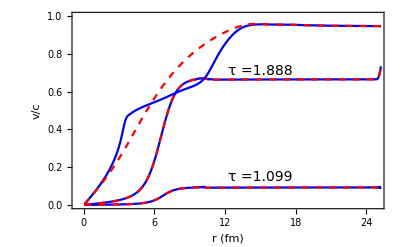

```mathematica
tmp=2;
t1 = times⟦tmp⟧;
p1=ListLinePlot[{vlists⟦tmp⟧,vlists0⟦tmp⟧},PlotStyle->{{Blue},{Red,Dashed}}, FrameLabel->{Style["r (fm)",16],Style["v/c",16]},PlotRange->{{-.5,25},{0,1}}];
txt1 = Graphics[
{Text[
Style["τ ="<>ToString[t1],14],{15,0.15},{0,0}
]}
];

tmp=10;
t2 = times⟦tmp⟧;
p2=ListLinePlot[{vlists⟦tmp⟧,vlists0⟦tmp⟧},PlotStyle->{{Blue},{Red,Dashed}}, FrameLabel->{Style["r (fm)",16],Style["v/c",16]},PlotRange->{{-.5,25},{0,1}}];
txt2 = Graphics[
{Text[
Style["τ ="<>ToString[t2],14],{15,0.71},{0,0}
]}
];

tmp=100;
t3 = times⟦tmp⟧;
p3=ListLinePlot[{vlists⟦tmp⟧,vlists0⟦tmp⟧},PlotStyle->{{Blue},{Red,Dashed}}, FrameLabel->{Style["r (fm)",16],Style["v/c",16]},PlotRange->{{-.5,25},{0,1}}];
txt3 = Graphics[
{Text[
Style["τ ="<>ToString[t3],14],{15,0.71},{0,0}
]}
];
Show[{p1,txt1, p2, txt2, p3}]
```

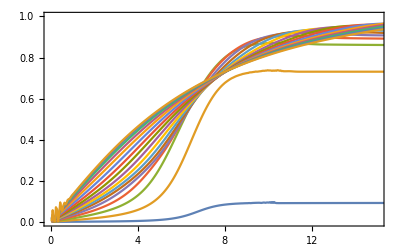

```mathematica
ListLinePlot[vlists0⟦2;;;;10⟧,PlotRange->{{0,15},{0,1}}]
```

### ϕ movies

Self-Consistency Check:  Show that modes below Q=ξ^-1don’t contribute to our integrals.
How sensitive are our results to the IR cutoff (lowest few modes?)

```mathematica
Dimensions[ϕfiles]
```

{0}

```mathematica
Nq = 100;
mode=1;

ϕeqLists = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfiles⟦2;;⟧}];
(*ϕeqLists0 = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfiles0⟦2;;⟧}];*)

ϕLists = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode+1]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfiles⟦2;;⟧}];
ϕLists0 = Table[ReadList["!awk '{print $1, $"<>ToString[3*mode+1]<>"}' "<>ToString[file],{Number,Number}],{file,ϕfiles0⟦2;;⟧}];

max2=Max[ϕeqLists⟦1,All,2⟧]*1.2;
 Animate[ListLinePlot[{ϕLists⟦i⟧,ϕeqLists⟦i⟧},PlotLabel->Style["τ = "<>ToString[ϕTimes⟦i⟧]<>", Mode "<>ToString[mode],20],
PlotStyle->{{Red,Thick,Dashed},{Blue,Thick}},
PlotRange->{{-.5,15},{0,max2}},FrameLabel->{Style["r (fm)",16],Style["ϕs",16]},
PlotLegends->{"ϕ backreaction","ϕ no backreaction"}],{i,1,Length[ϕLists],1},AnimationRate->16,AnimationRunning->False]

(*Animate[ListLinePlot[ϕeqLists⟦i⟧,PlotLabel->Style["τ = "<>ToString[ϕTimes⟦i⟧]<>", Mode "<>ToString[mode],20],
PlotStyle->{{Red,Thick,Dashed},{Blue,Thick}},
PlotRange->{{-.5,15},{0,max2}},FrameLabel->{Style["r (fm)",16],Style["ϕs",16]},PlotLegends->{"ϕ_eq backreaction","ϕ_eq no backreaction"}],{i,1,Length[ϕeqLists],1},AnimationRate->16,AnimationRunning->False]*)

max3=Max[ϕLists⟦-2,All,2⟧/ϕeqLists⟦-2,All,2⟧]*1.15;
max3=6;
ratio1Ani=Animate[ListLinePlot[Transpose[{ϕLists⟦i,All,1⟧,ϕLists⟦i,All,2⟧/ϕeqLists⟦i,All,2⟧}],PlotLabel->Style["τ = "<>ToString[ϕTimes⟦i⟧]<>", Mode "<>ToString[mode],20],
PlotStyle->{Blue,Thick},
PlotRange->{{-.5,15},{0,max3}},FrameLabel->{Style["r (fm)",16],Style["ϕ/ϕ_0",16]},
GridLines->{None,{{1,Dashed}}}],{i,1,Length[ϕLists],1},AnimationRate->16,AnimationRunning->False]
```

### p, p_(+), D_r p_(+)

Re-organize data

```mathematica
plists = Table[ReadList["!awk '{print $1, $2}' "<>ToString[file],{Number,Number}],{file,pfiles⟦5;;⟧}];
(*plists0 = Table[ReadList["!awk '{print $1, $2}' "<>ToString[file],{Number,Number}],{file,pfiles0⟦5;;⟧}];*)
ppluslists = Table[ReadList["!awk '{print $1, $3}' "<>ToString[file],{Number,Number}],{file,pfiles⟦5;;⟧}];
(*ppluslists0 = Table[ReadList["!awk '{print $1, $3}' "<>ToString[file],{Number,Number}],{file,pfiles0⟦5;;⟧}];*)
Dplists = Table[ReadList["!awk '{print $1, $4}' "<>ToString[file],{Number,Number}],{file,pfiles⟦5;;⟧}];
Dppluslists = Table[ReadList["!awk '{print $1, $5}' "<>ToString[file],{Number,Number}],{file,pfiles⟦5;;⟧}];
max4 = Max[{Max[plists⟦1,2;;,2⟧],Max[ppluslists⟦1,2;;,2⟧]}];
min = Min[{Min[plists⟦1,2;;,2⟧],Min[ppluslists⟦1,2;;,2⟧]}];
```

p, p_(+), and residual plots

Figure out why p and p_(+) don’t start out exactly the same at the start of the movie

```mathematica
pAni=Animate[ListLinePlot[{ppluslists⟦i,2;;⟧,plists⟦i,2;;⟧},
PlotStyle->{{Blue,Thick},{Red}},
PlotLabel->Style["p_(+) vs. p, τ = "<>ToString[ϕTimes⟦i⟧],20],PlotRange->{{-.5,15},{min,max4}},
FrameLabel->{Style["r (fm)",16],Style["p (GeV^4)",16]},PlotLegends->{"p_(+)","p"}],{i,1,Length[plists],1},AnimationRate->4,AnimationRunning->False]

(*pAni=Animate[ListLinePlot[{ppluslists⟦i,2;;⟧,ppluslists0⟦i,2;;⟧},
PlotStyle->{{Blue,Thick},{Red}},
PlotLabel->Style["p_(+) vs. p, τ = "<>ToString[ϕTimes⟦i⟧],20],PlotRange->{{-.5,15},{0,max4}},
FrameLabel->{Style["r (fm)",16],Style["p (GeV^4)",16]},PlotLegends->{"p_(+) backreact","p_(+) no backreact"}],{i,1,Length[plists],1},AnimationRate->16,AnimationRunning->False]*)

residualAni=Animate[ListLinePlot[Transpose[{ppluslists⟦i,2;;,1⟧,(ppluslists⟦i,2;;,2⟧-plists⟦i,2;;,2⟧)/plists⟦i,2;;,2⟧}],PlotLabel->Style["residual",20],
PlotStyle->{Blue,Thick},
PlotRange->{{-.5,15},{-.01,.02}},
FrameLabel->{Style["r (fm)",16],Style["(p_(+) - p)/p",6]}],{i,1,Length[plists],1},AnimationRate->4,AnimationRunning->False]
```

Double check that Drp_(+) is computed correctly

```mathematica
fac=5.06842;
Animate[ListLinePlot[{Thread[{ppluslists⟦i,3;;,1⟧,Differences[ppluslists⟦i,2;;,2⟧]/Differences[ppluslists⟦i,2;;,1⟧]}],
Thread[{plists⟦i,3;;,1⟧,Differences[plists⟦i,2;;,2⟧]/Differences[plists⟦i,2;;,1⟧]}],
{#⟦1⟧,#⟦2⟧*fac}&/@Dplists⟦i⟧,
{#⟦1⟧,#⟦2⟧*fac}&/@Dppluslists⟦i⟧},
PlotLabel->Style["Numerical Drp_(+) vs. Drp, Analytic τ = "<>ToString[ϕTimes⟦i⟧],18],
PlotStyle->{{Blue,Thick},{Blue,Dashed,Thick},{Green, Dashed},{Green}},
(*PlotRange->{{-.5,15},{-.0015,.0001}},*)
FrameLabel->{Style["r (fm)",16],Style["Drp",6]},
PlotLegends->{"Numerical Drp_(+)","Numerical Drp", "Drp", "Drp_(+)"}],{i,1,Length[ppluslists],1},AnimationRunning->False,AnimationRate->16]
```